```mathematica
pts=RandomPoint[Disk[],25];
```

```mathematica
boundary = {{-1,1},{-1,1}};
```

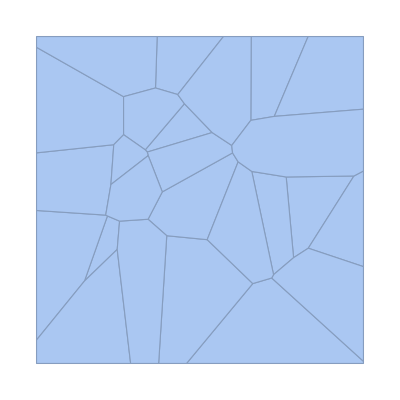

```mathematica
vMesh=VoronoiMesh[pts,boundary]
```

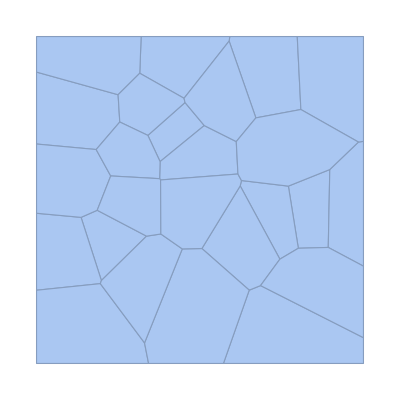
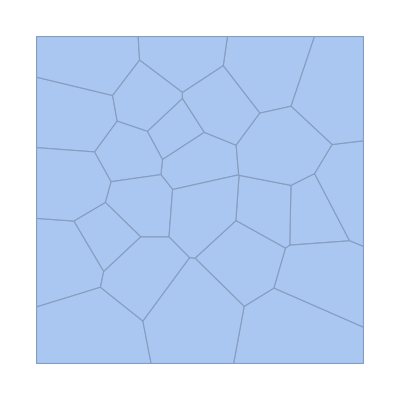
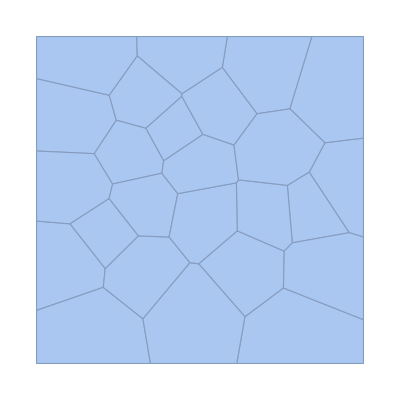
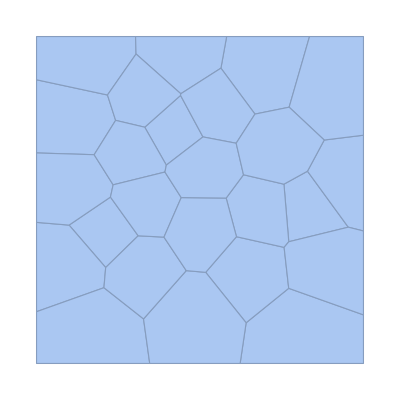
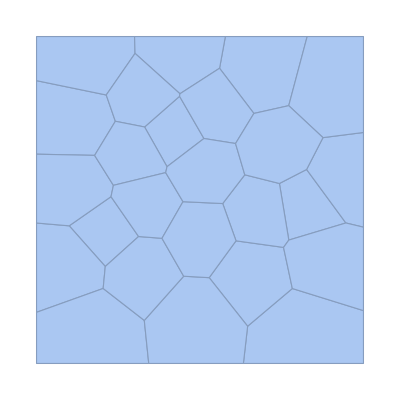
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
vml=NestList[VoronoiMesh[Mean@@@MeshPrimitives[#,2],boundary]&,vMesh,5]
```

```mathematica
finalMesh=Last@vml
```

-Graphics-

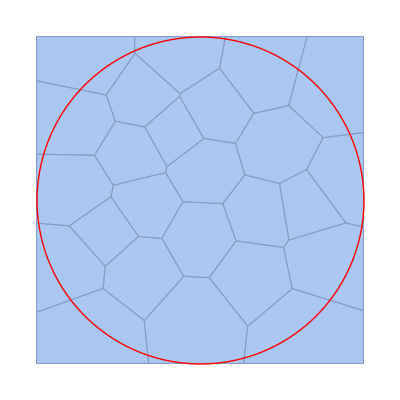

```mathematica
Show[finalMesh,Graphics[{Red,Thick,Circle[]}]]
```

```mathematica
grains=MeshPrimitives[finalMesh,2];
```

```mathematica
Offset
```

```mathematica
grainsCoord=Flatten[Union[Table[Cases[grains[[i]],Repeated[_,10]],{i,Length[grains]}]],1];
```

```mathematica
Length[grains]==Length[grainsCoord]
```

True

```mathematica
nodes=Flatten[Cases[#,{_,_}]&/@MeshPrimitives[finalMesh,0],1];
```

```mathematica
edges=Flatten[Cases[#,{_,_}]&/@MeshPrimitives[finalMesh,1],1];
```

```mathematica
assoc=Association[Table[nodes[[i]]->i,{i,Length[nodes]}]];
```

```mathematica
edges/.Normal[assoc];
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
bmesh=ToBoundaryMesh["Coordinates"->nodes,"BoundaryElements"->{LineElement[edges/.Normal[assoc]]}]
```

ElementMesh[{{-1.,1.},{-1.,1.}},Automatic]

```mathematica
RegionBounds[finalMesh]
```

{{-1.,1.},{-1.,1.}}

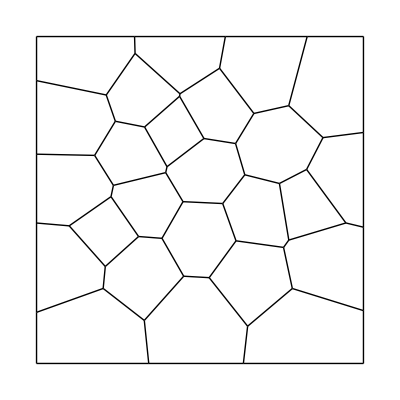

```mathematica
Show[bmesh["Wireframe"]]
```

```mathematica
mesh=ToElementMesh[bmesh,"MeshOrder"->1,"MeshElementConstraint"->30,MaxCellMeasure->{"Length"->.15}]
```

ElementMesh[{{-1.,1.},{-1.,1.}},{TriangleElement[<1397>]}]

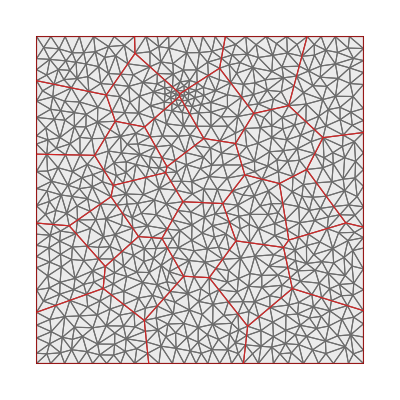

```mathematica
Show[mesh["Wireframe"],Graphics[{EdgeForm[{Red,Thick}],Opacity[0.5],LightGray,grains}]]
```

```mathematica
mesh["Properties"]
```

{BoundaryConnectivity,BoundaryElements,Bounds,ContinuousElementConnectivity,Coordinates,ElementConnectivity,EmbeddingDimension,HangingNodes,MeshElements,MeshOrder,PointElements,Properties,Quality,RegionHoles,VertexBoundaryConnectivity,VertexElementConnectivity}

```mathematica
meshTRIAcoord=mesh["Coordinates"];
```

```mathematica
numNode=Length@meshTRIAcoord
```

744

```mathematica
meshTRIAconnect=Join@@ElementIncidents[mesh["MeshElements"]];
```

```mathematica
numElements=Length@meshTRIAconnect
```

1397

```mathematica
numeGrains=Length@grainsCoord
```

25

```mathematica
indexCenter[indexList_]:= Mean[meshTRIAcoord[[#]]&/@indexList]
```

## Convert the mesh: triangles to quadrilaterals

```mathematica
subsequence[1]={{1,2},{2,3},{3,1}}
```

{{1,2},{2,3},{3,1}}

```mathematica
subsequence[i_]:=(subsequence[i]=Module[{previousSequenceFirst=First[subsequence[i-1]][[1]],previousSequenceLast=Last[subsequence[i-1]][[1]]},{{previousSequenceLast+1,previousSequenceLast+2},{previousSequenceLast+2,previousSequenceLast+3},{previousSequenceLast+3,previousSequenceLast+1}}])

icount=1;
sequencesAt=NestList[(icount++;Join[#,subsequence[icount]])&,subsequence[1],1500];
```

```mathematica
edgesSequence=sequencesAt[[numElements]];
```

```mathematica
edges=Partition[Flatten[meshTRIAconnect][[Flatten[edgesSequence]]],2];
```

```mathematica
midpoints= Partition[indexCenter/@edges,3];
```

```mathematica
elementCenters=indexCenter/@meshTRIAconnect;
```

```mathematica
elementNodesXYZ = meshTRIAcoord[[#]]&/@meshTRIAconnect;
```

```mathematica
quad1=Table[Polygon[{midpoints[[i,3]],elementNodesXYZ[[i,1]],midpoints[[i,1]],elementCenters[[i]]}],{i,1,numElements}];
```

```mathematica
quad2=Table[Polygon[{midpoints[[i,1]],elementNodesXYZ[[i,2]],midpoints[[i,2]],elementCenters[[i]]}],{i,1,numElements}];
```

```mathematica
quad3=Table[Polygon[{midpoints[[i,2]],elementNodesXYZ[[i,3]],midpoints[[i,3]],elementCenters[[i]]}],{i,1,numElements}];
```

```mathematica
midpointsList=Flatten[midpoints,1];
```

```mathematica
newNodes = Join[midpointsList,elementCenters];
```

```mathematica
newNodesNumber=Max[Flatten[meshTRIAconnect]]+ Range[Length[midpointsList]+Length[elementCenters]];
```

```mathematica
newNodeRules = Thread[Rule[newNodes,newNodesNumber]];
```

```mathematica
quad1Incidence=Table[{midpoints[[i,3]]/.newNodeRules,meshTRIAconnect[[i,1]],midpoints[[i,1]]/.newNodeRules,elementCenters[[i]]/.newNodeRules},{i,1,numElements}];
```

```mathematica
quad2Incidence=Table[{midpoints[[i,1]]/.newNodeRules,meshTRIAconnect[[i,2]],midpoints[[i,2]]/.newNodeRules,elementCenters[[i]]/.newNodeRules},{i,1,numElements}];
```

```mathematica
quad3Incidence=Table[{midpoints[[i,2]]/.newNodeRules,meshTRIAconnect[[i,3]],midpoints[[i,3]]/.newNodeRules,elementCenters[[i]]/.newNodeRules},{i,1,numElements}];
```

```mathematica
allNodes=Join[meshTRIAcoord,newNodes];
```

```mathematica
allNodesNumbered=Partition[Flatten[Riffle[Range[Length[allNodes]],allNodes]],3];
```

```mathematica
Dimensions[allNodesNumbered]
```

{6332,3}

```mathematica
quadElements=Join[quad1Incidence,quad2Incidence,quad3Incidence];
```

```mathematica
numQuadElem=Length@quadElements
```

4191

```mathematica
quadElementsNumbered=Partition[Flatten[Riffle[Range[Length[quadElements]],quadElements]],5];
```

```mathematica
Export[NotebookDirectory[]<>"nodesPolycrystal_2Drectangle.csv",allNodes]
```

/Users/gio/Dropbox (MIT)/Anisotropy_NMCparticle/nodesPolycrystal_2Drectangle.csv

```mathematica
Export[NotebookDirectory[]<>"elementsPolycrystal_2Drectangle.csv",quadElements]
```

/Users/gio/Dropbox (MIT)/Anisotropy_NMCparticle/elementsPolycrystal_2Drectangle.csv

## Assign a grain to each finite element (grains will be treated as material IDs)

```mathematica
quadElementCenters =Mean[#]&/@(allNodes[[#]]&/@quadElements);
```

```mathematica
Length[quadElementCenters]
```

4191

```mathematica
ℛ=Polygon[#]&/@grainsCoord;
```

```mathematica
mf=RegionMember[#]&/@ℛ;
```

```mathematica
mf[[1]][elementCenters[[1]]]
```

False

```mathematica
elementsPosition=Table[Table[mf[[i]][quadElementCenters[[j]]],{i,1,numeGrains}],{j,1,numQuadElem}];
```

```mathematica
Dimensions@elementsPosition
```

{4191,25}

```mathematica
testOnElemPosition=Flatten@Table[Position[elementsPosition[[i]],True],{i,numQuadElem}];
```

```mathematica
Flatten[Position[testOnElemPosition,1]]
```

{7,8,19,236,374,377,378,381,452,456,457,461,462,566,567,568,569,570,571,573,574,577,578,786,790,791,842,843,1222,1223,1404,1405,1416,1633,1771,1774,1775,1778,1849,1853,1854,1858,1859,1963,1964,1965,1966,1967,1968,1970,1971,1974,1975,2183,2187,2188,2239,2240,2619,2620,2801,2802,2813,3030,3168,3171,3172,3175,3246,3250,3251,3255,3256,3360,3361,3362,3363,3364,3365,3367,3368,3371,3372,3580,3584,3585,3636,3637,4016,4017}

```mathematica
elementsGrain=Table[allNodes[[#]]&/@( quadElements[[#]]&/@Flatten[Position[testOnElemPosition,i]]),{i,numeGrains}];
```

```mathematica
coordelementsGrain=Table[allNodes[[#]]&/@elementsGrain[[i]],{i,numeGrains}];
```

Part::pkspec1: The expression {{-0.576355,-0.00186038},{-0.608341,-0.0241652},{-0.55858,-0.0275631},{-0.553843,-0.0115606}} cannot be used as a part specification.

Part::pkspec1: The expression {{-0.640327,-0.04647},{-0.672314,-0.0687748},{-0.654863,-0.0944786},{-0.639356,-0.0710408}} cannot be used as a part specification.

Part::pkspec1: The expression {{-0.779513,-0.181364},{-0.758767,-0.204734},{-0.75388,-0.163489},{-0.76934,-0.161657}} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
colorList=Join[ColorData[1,"ColorList"],ColorData[2,"ColorList"],ColorData[3,"ColorList"]]
```

{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6],RGBColor[0.6, 0.24, 0.5632658430022722],RGBColor[0.6, 0.42664098839727194, 0.24],RGBColor[0.2634521802031821, 0.6, 0.24],RGBColor[0.24, 0.47354534880363613, 0.6],RGBColor[0.5163614825959097, 0.24, 0.6],RGBColor[0.6, 0.3062683139954558, 0.24],RGBColor[0.3838248546049982, 0.6, 0.24],RGBColor[0.24, 0.5939180232054561, 0.6],RGBColor[0.39598880819409377, 0.24, 0.6],RGBColor[0.6, 0.24, 0.2941043604063603],RGBColor[0.8588235294117647, 0.00784313725490196, 0.00784313725490196],RGBColor[1., 0.26666666666666666, 0.],RGBColor[1., 0.4549019607843137, 0.2549019607843137],RGBColor[0.4823529411764706, 0.18823529411764706, 0.03529411764705882],RGBColor[1., 0.8784313725490196, 0.5058823529411764],RGBColor[0.7019607843137254, 0.7450980392156863, 0.8235294117647058],RGBColor[0.20784313725490197, 0.23921568627450981, 0.3215686274509804],RGBColor[0.08627450980392157, 0.1411764705882353, 0.28627450980392155],RGBColor[0.33725490196078434, 0.403921568627451, 0.6235294117647059],RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}

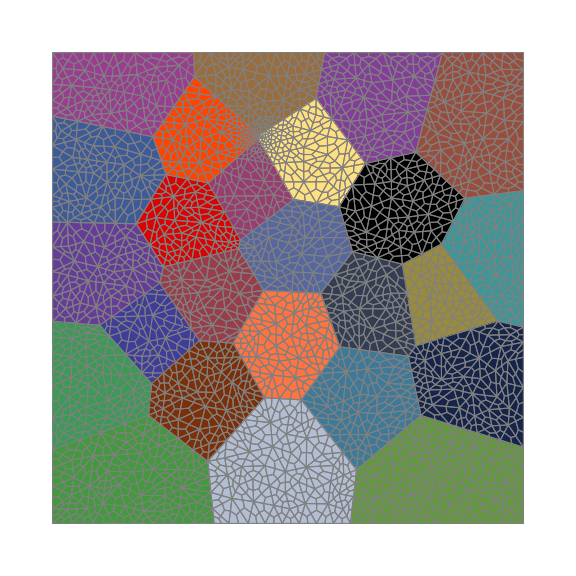

```mathematica
Show[Graphics[Table[{EdgeForm[Gray],colorList[[i]],Polygon[#]&/@elementsGrain[[i]]},{i,numeGrains}]],ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"GrainID.tsv",testOnElemPosition-1]
```

/Users/gio/Dropbox (MIT)/Anisotropy_NMCparticle/GrainID.csv

```mathematica
firstCrystalDir=Table[{Cos[#],Sin[#]}&[RandomReal[{0,2Pi}]],{grains}]
```

{{0.339937,0.940448},{-0.105912,0.994376},{-0.72459,-0.689181},{0.781554,-0.623838},{0.261629,-0.965169},{-0.723645,-0.690173},{0.974907,-0.222614},{0.493196,0.869918},{0.225734,-0.974189},{0.994801,0.101835},{0.917931,-0.39674},{-0.739456,0.673205},{0.286221,-0.958164},{-0.710269,-0.70393},{-0.173426,0.984847},{-0.986904,-0.161307},{0.262165,0.965023},{0.602561,-0.798073},{0.654376,-0.756169},{-0.900973,0.433876},{0.786385,-0.617736},{-0.91258,-0.408898},{0.872426,0.488746},{0.121257,-0.992621},{-0.57804,-0.816009}}

```mathematica
secondCrystalDir=Cross[#]&/@firstCrystalDir
```

{{-0.940448,0.339937},{-0.994376,-0.105912},{0.689181,-0.72459},{0.623838,0.781554},{0.965169,0.261629},{0.690173,-0.723645},{0.222614,0.974907},{-0.869918,0.493196},{0.974189,0.225734},{-0.101835,0.994801},{0.39674,0.917931},{-0.673205,-0.739456},{0.958164,0.286221},{0.70393,-0.710269},{-0.984847,-0.173426},{0.161307,-0.986904},{-0.965023,0.262165},{0.798073,0.602561},{0.756169,0.654376},{-0.433876,-0.900973},{0.617736,0.786385},{0.408898,-0.91258},{-0.488746,0.872426},{0.992621,0.121257},{0.816009,-0.57804}}

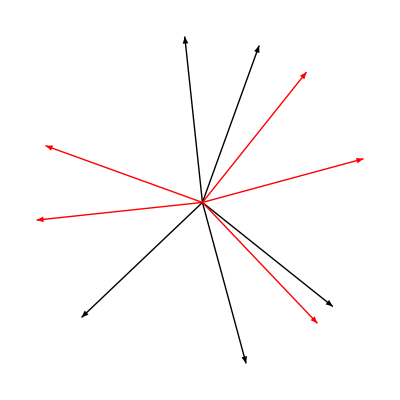

```mathematica
Graphics[{{Table[Arrow[{{0,0},firstCrystalDir[[i]]}],{i,5}]},{Red,Table[Arrow[{{0,0},secondCrystalDir[[i]]}],{i,5}]}}]
```

```mathematica
orthoNormVectors=Riffle[firstCrystalDir,secondCrystalDir];
```

```mathematica
Export[NotebookDirectory[]<>"grainCrystalOrient.tsv",orthoNormVectors]
```

/Users/gio/Dropbox (MIT)/Anisotropy_NMCparticle/grainCrystalOrient.tsv